## DelaunayPairs-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 05:05:49
using xCellerator 0.90 and XSSA 1204002

Create a tissue with a point and an edge that aren't used.

```mathematica
r:=RandomReal[{0, 10}]; 
v=Table[{r,r}, {100}];
```

```mathematica
de=DelaunayEdges[v];
```

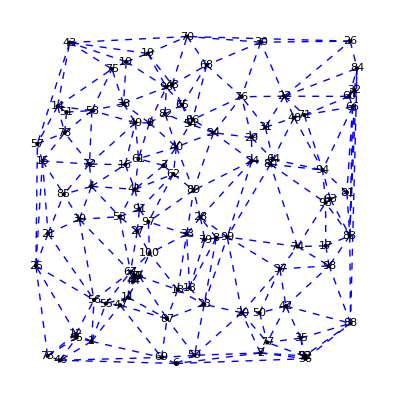

```mathematica
Show[Graphics[{Blue, Dashed, Line/@de}], Graphics[Point/@v] , 
Graphics[MapThread[Text[ToString[#1], #2]&, {Range[Length[v]], v}]],
 BaseStyle-> {FontSize-> 16, FontColor-> Red}]
```

```mathematica
DelaunayPairs[v]
```

{{1,12},{1,46},{1,47},{1,55},{1,56},{1,69},{1,95},{2,6},{2,20},{2,36},{2,52},{2,59},{2,77},{3,40},{3,41},{3,61},{3,62},{4,16},{4,39},{4,41},{4,53},{4,72},{4,85},{5,11},{5,18},{5,44},{5,67},{5,87},{5,90},{5,100},{6,36},{6,46},{6,59},{6,69},{7,44},{7,67},{7,90},{8,13},{8,23},{8,28},{8,79},{8,99},{9,38},{9,40},{9,49},{9,61},{9,82},{9,96},{10,19},{10,38},{10,43},{10,75},{10,96},{11,44},{11,47},{11,55},{11,67},{11,87},{12,25},{12,56},{12,73},{12,95},{13,18},{13,23},{13,33},{13,79},{14,43},{14,51},{14,57},{14,58},{14,75},{14,78},{15,21},{15,25},{15,57},{15,72},{15,78},{15,85},{16,41},{16,49},{16,61},{16,72},{17,74},{17,83},{17,93},{17,98},{18,23},{18,33},{18,87},{18,100},{19,43},{19,45},{19,70},{19,96},{20,23},{20,37},{20,50},{20,59},{20,77},{20,99},{21,25},{21,39},{21,56},{21,85},{22,26},{22,30},{22,31},{22,48},{22,60},{22,71},{22,76},{22,84},{23,59},{23,87},{23,99},{24,28},{24,29},{24,34},{24,64},{24,80},{24,89},{24,99},{25,56},{25,57},{25,73},{26,30},{26,70},{26,84},{27,53},{27,67},{27,91},{27,97},{27,100},{28,33},{28,79},{28,89},{28,99},{29,31},{29,34},{29,64},{29,76},{30,68},{30,70},{30,76},{31,48},{31,64},{31,76},{32,60},{32,66},{32,83},{32,84},{33,79},{33,89},{33,97},{33,100},{34,40},{34,54},{34,76},{34,86},{34,89},{35,42},{35,52},{35,77},{35,88},{35,92},{36,52},{36,88},{36,92},{37,42},{37,50},{37,74},{37,98},{37,99},{38,49},{38,58},{38,75},{38,96},{39,53},{39,56},{39,67},{39,85},{40,54},{40,61},{40,62},{40,82},{40,89},{41,53},{41,61},{41,62},{41,91},{42,50},{42,77},{42,88},{42,98},{43,57},{43,70},{43,75},{44,67},{44,90},{45,65},{45,68},{45,70},{45,96},{46,69},{46,73},{46,95},{47,55},{47,69},{47,87},{48,64},{48,71},{48,94},{49,58},{49,61},{49,72},{50,77},{51,58},{51,78},{52,77},{52,92},{53,67},{53,91},{54,65},{54,82},{54,86},{55,56},{55,67},{56,67},{57,78},{58,72},{58,75},{58,78},{59,69},{59,87},{60,66},{60,71},{60,84},{62,89},{62,91},{62,97},{63,81},{63,83},{63,93},{63,94},{64,80},{64,94},{65,68},{65,82},{65,86},{65,96},{66,71},{66,81},{66,83},{66,94},{67,90},{67,100},{68,70},{68,76},{68,86},{69,87},{71,94},{72,78},{72,85},{73,95},{74,80},{74,93},{74,98},{74,99},{76,86},{80,93},{80,94},{80,99},{81,83},{81,94},{82,96},{83,84},{83,88},{83,93},{83,98},{84,88},{88,92},{88,98},{89,97},{91,97},{93,94},{97,100}}